## Qn 1 (a)

```mathematica
MomentGeneratingFunction[NormalDistribution[3,2],t]
```

ⅇ^(3 t+2 t^2)

## Qn 1 (b)

```mathematica
MomentGeneratingFunction[TransformedDistribution[5X1-2X2+6,{X1\[Distributed]NormalDistribution[3,2],X2\[Distributed]NormalDistribution[3,2]}],t]
```

ⅇ^(15 t+58 t^2)

## Qn 2 (a)

PDF of Average

```mathematica
12*PDF[UniformSumDistribution[12],x]/. {x-> y*12}
```

12 (Piecewise[{{0, 12 y<0}, {(35831808 y^11)/1925, 0≤12 y<1}, {(743008370688 y^11-12 (-1+12 y)^11)/39916800, 1≤12 y<2}, {(743008370688 y^11+66 (-2+12 y)^11-12 (-1+12 y)^11)/39916800, 2≤12 y<3}, {(743008370688 y^11-220 (-3+12 y)^11+66 (-2+12 y)^11-12 (-1+12 y)^11)/39916800, 3≤12 y<4}, {(743008370688 y^11+495 (-4+12 y)^11-220 (-3+12 y)^11+66 (-2+12 y)^11-12 (-1+12 y)^11)/39916800, 4≤12 y<5}, {(743008370688 y^11-792 (-5+12 y)^11+495 (-4+12 y)^11-220 (-3+12 y)^11+66 (-2+12 y)^11-12 (-1+12 y)^11)/39916800, 5≤12 y<6}, {(-792 (7-12 y)^11+495 (8-12 y)^11-220 (9-12 y)^11+66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11)/39916800, 6≤12 y<7}, {(495 (8-12 y)^11-220 (9-12 y)^11+66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11)/39916800, 7≤12 y<8}, {(-220 (9-12 y)^11+66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11)/39916800, 8≤12 y<9}, {(66 (10-12 y)^11-12 (11-12 y)^11+(12-12 y)^11)/39916800, 9≤12 y<10}, {(-12 (11-12 y)^11+(12-12 y)^11)/39916800, 10≤12 y<11}, {(12-12 y)^11/39916800, 11≤12 y≤12}, {0, True}}])

Plot of PDF of Average

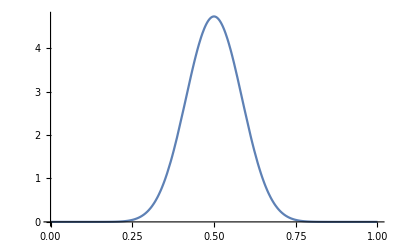

```mathematica
Plot[12*Evaluate[PDF[UniformSumDistribution[12],x] /. {x -> y*12}], {y,0,1}]
```

## Qn 2 (b)

```mathematica
N[Probability[6≤x≤8, x\[Distributed] UniformSumDistribution[12]]]
```

0.477724

Alternative method for same calculation

```mathematica
N[CDF[UniformSumDistribution[12],8] -CDF[UniformSumDistribution[12],6]]
```

0.477724

## Qn 2 (c)

```mathematica
N[Probability[1/2≤x≤2/3, x\[Distributed] NormalDistribution[1/2,1/12]]]
```

0.47725

Aternative method for approximation

```mathematica
N[CDF[NormalDistribution[1/2,1/12],2/3] -CDF[NormalDistribution[1/2,1/12],1/2]]
```

0.47725

## Qn 3 (a)

```mathematica
t1 = TransformedDistribution[U^(1/3),U \[Distributed] UniformDistribution[]]
```

BetaDistribution[3,1]

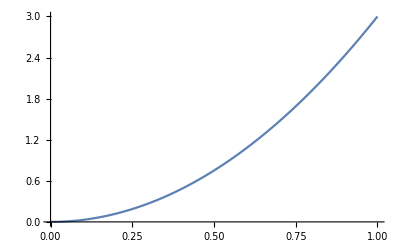

```mathematica
Plot[PDF[t1,x],{x,0,1}]
```

```mathematica
Mean[t1]
```

3/4

```mathematica
Variance[t1]
```

3/80

## Qn 3 (b)

```mathematica
tf=TransformedDistribution[A+B + C + D,{A\[Distributed]t1,B\[Distributed]t1,C \[Distributed] t1,D \[Distributed] t1}]
```

TransformedDistribution[x1+x2+x3+x4,{x1\[Distributed]BetaDistribution[3,1],x2\[Distributed]BetaDistribution[3,1],x3\[Distributed]BetaDistribution[3,1],x4\[Distributed]BetaDistribution[3,1]}]

```mathematica
ee= PDF[tf]
```

Function[x,1/61600(415800 (-4+x)^3 Sign[-4+x]+831600 (-4+x)^4 Sign[-4+x]+665280 (-4+x)^5 Sign[-4+x]+277200 (-4+x)^6 Sign[-4+x]+67320 (-4+x)^7 Sign[-4+x]+9900 (-4+x)^8 Sign[-4+x]+880 (-4+x)^9 Sign[-4+x]+44 (-4+x)^10 Sign[-4+x]+(-4+x)^11 Sign[-4+x]-166320 (-3+x)^5 Sign[-3+x]-166320 (-3+x)^6 Sign[-3+x]-71280 (-3+x)^7 Sign[-3+x]-15840 (-3+x)^8 Sign[-3+x]-1980 (-3+x)^9 Sign[-3+x]-132 (-3+x)^10 Sign[-3+x]-4 (-3+x)^11 Sign[-3+x]+11880 (-2+x)^7 Sign[-2+x]+5940 (-2+x)^8 Sign[-2+x]+1320 (-2+x)^9 Sign[-2+x]+132 (-2+x)^10 Sign[-2+x]+6 (-2+x)^11 Sign[-2+x]-220 (-1+x)^9 Sign[-1+x]-44 (-1+x)^10 Sign[-1+x]-4 (-1+x)^11 Sign[-1+x]+x^11 Sign[x])]

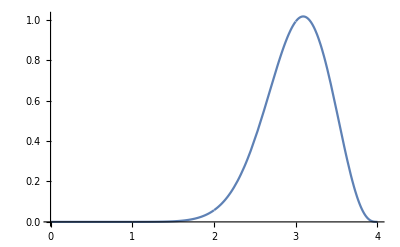

```mathematica
Plot[ee[x],{x,0,4}]
```

## Qn 3 (c)

```mathematica
N[CDF[ tf,1.5]- CDF[ tf,0.3]]
```

0.000350282

## Qn 3 (d)

```mathematica
Mean[tf]
```

3

```mathematica
Variance[tf]
```

3/20

```mathematica
N[CDF[ NormalDistribution[3,√0.15],1.5]- CDF[ NormalDistribution[3,√0.15],0.3]]
```

0.0000537556

## Qn 4

```mathematica
Mean[GammaDistribution[α,1]]
```

α

```mathematica
Variance[GammaDistribution[α,1]]
```

α

```mathematica
Manipulate[lower= Max[0, α-5*√α];
		upper =α+5*√α;		
 mpd = 0.5*(NIntegrate[Abs[PDF[GammaDistribution[α,1],x]-PDF[NormalDistribution[α,√α],x]],{x,lower,upper},AccuracyGoal->5]+ CDF[NormalDistribution[α,√α],lower]+CDF[GammaDistribution[α,1],lower]+1-CDF[NormalDistribution[α,√α],upper]+ 1-CDF[GammaDistribution[α,1],upper]);
		postext = {1.0,1.0};
	 Show[Plot[{PDF[GammaDistribution[α,1],x],PDF[NormalDistribution[α,√α],x]},{x,lower,upper},PlotRange -> Full,AxesLabel->{"x","pdf(x)"},BaseStyle->Large,PlotLegends->Placed[{Style["Gamma",24],Style["Normal",24]},Above], PlotStyle -> AbsoluteThickness[3]],
Graphics[Style[Text["α ="<>ToString[ScientificForm[α,3],TraditionalForm],Scaled[{postext[[1]],postext[[2]]}],Offset[{-1,0}]],20]
],
	Graphics[Style[Text[" D ="<>ToString[ScientificForm[mpd,3],TraditionalForm],Scaled[{postext[[1]],postext[[2]]-0.06}],Offset[{-1,0}]],20]
],ImageSize -> Large]
	,
{α,1,150,1}]
```